```mathematica
RepresentArrays[array1_,array2_]:=Module[{rows,cols,grid},{rows,cols}=Dimensions[array1];
grid=Table[Style[Rectangle[{i,j},{i-1+spacing,j-1+spacing}],EdgeForm[{Thickness[0.03],ColorData["Rainbow"][Rescale[array1[[i,j]],{Min[array1],Max[array1]}]]}],ColorData["Rainbow"][Rescale[array2[[i,j]],{Min[array2],Max[array2]}]]],{i,1,rows},{j,1,cols}];
(*Return the grid as a graphic*)Graphics[grid,PlotRange->{{0,rows},{0,cols}},AspectRatio->1]]
```

```mathematica
(*Example arrays*)
array1=RandomReal[{0,2},{5,5}]
array2=ArrayReshape[Subdivide[0,1,24],{5,5}]
array3=RandomReal[{0,1},{5,5}]
```

{{1.17144,1.86822,0.0233149,0.553439,1.04846},{1.91755,0.471021,1.31295,0.394991,1.32663},{0.861848,1.89815,1.83794,1.68778,0.476564},{1.34435,0.302679,0.970487,0.756622,0.0890001},{1.08077,0.700767,0.910028,0.630613,1.5515}}

{{0,1/24,1/12,1/8,1/6},{5/24,1/4,7/24,1/3,3/8},{5/12,11/24,1/2,13/24,7/12},{5/8,2/3,17/24,3/4,19/24},{5/6,7/8,11/12,23/24,1}}

{{0.359751,0.544817,0.348166,0.305316,0.485897},{0.0580211,0.0766691,0.235192,0.23741,0.301558},{0.740219,0.147339,0.955401,0.701904,0.201012},{0.121691,0.770067,0.704788,0.739258,0.909791},{0.0743571,0.753847,0.424266,0.817413,0.153177}}

```mathematica
(*Plot the arrays*)
spacing=0.15;
g=RepresentArrays[array1,array2];
```

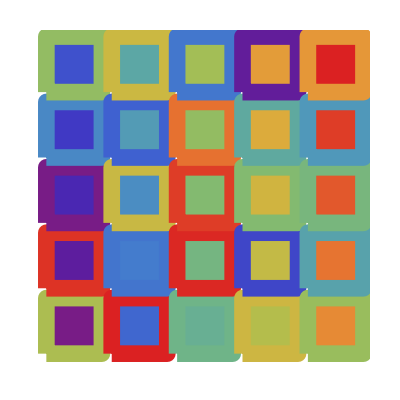

```mathematica
Rotate[g,-1.5708]
```